## Import data files and create interpolation objects

Native Coulomb wave form factors span the range E = 1 eV to 109.648 eV and:
for 1a1, q = 1 to 100 keV;
for 2a1, q = 1 to 76.35 keV;
for 1t2, q = 1 to 38.89 keV.
q is the momentum transfer [in keV] and E is the electron kinetic energy [in keV].

For higher values of q than those above (where the form factor is very very small), we also give form factors where we match onto the (rescaled) plane wave results. The plots at the bottom of the notebook show this extrapolation.

### Coulomb wave

```mathematica
SetDirectory[NotebookDirectory[]];
LCH41agrid=Import["CH4_CW_1a_grid.dat"];
LCH42agrid=Import["CH4_CW_2a_grid.dat"];
LCH41tgrid=Import["CH4_CW_1t_grid.dat"];
ResetDirectory[];

fCH4CW1a=Interpolation[LCH41agrid,InterpolationOrder->1]
fCH4CW2a=Interpolation[LCH42agrid,InterpolationOrder->1]
fCH4CW1t=Interpolation[LCH41tgrid,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

### Coulomb wave + matched rescaled Plane wave at high q

```mathematica
SetDirectory[NotebookDirectory[]];
LCH4CWPW1agrid=Import["CH4_1a_grid_PW_largeQ.dat"];
LCH4CWPW2agrid=Import["CH4_2a_grid_PW_largeQ.dat"];
LCH4CWPW1tgrid=Import["CH4_1t_grid_PW_largeQ.dat"];
ResetDirectory[];

fCH4CWPW1a=Interpolation[LCH4CWPW1agrid,InterpolationOrder->1]
fCH4CWPW2a=Interpolation[LCH4CWPW2agrid,InterpolationOrder->1]
fCH4CWPW1t=Interpolation[LCH4CWPW1tgrid,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

### Plots

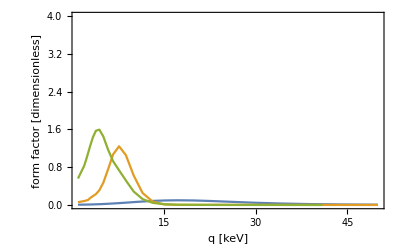

```mathematica
EtestkeV=0.025;

Plot[{fCH4CW1a[q,EtestkeV],fCH4CW2a[q,EtestkeV],fCH4CW1t[q,EtestkeV]},{q,1,50},PlotRange->{{1,50},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]
```

### Plots - showing the plane wave extrapolation in black

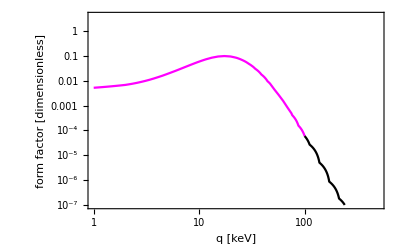

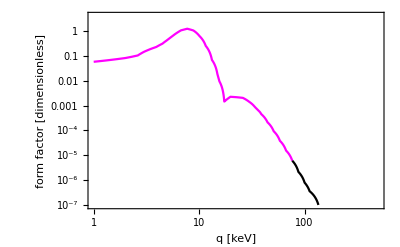

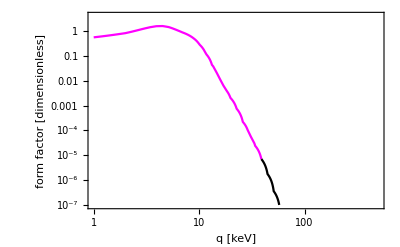

```mathematica
EtestkeV=0.025;

Show[LogLogPlot[{fCH4CW1a[q,EtestkeV]},{q,1,LCH41agrid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fCH4CWPW1a[q,EtestkeV]},{q,LCH41agrid[[-1,1]],500},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}]]

Show[LogLogPlot[{fCH4CW2a[q,EtestkeV]},{q,1,LCH42agrid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fCH4CWPW2a[q,EtestkeV]},{q,LCH42agrid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}]]

Show[LogLogPlot[{fCH4CW1t[q,EtestkeV]},{q,1,LCH41tgrid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fCH4CWPW1t[q,EtestkeV]},{q,LCH41tgrid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}]]
```